## Mathematica Computation of Magnetization Vector

## Computation (Cross Product -> NDSolver)

```mathematica
Inputs;
```

```mathematica
f=1;
```

```mathematica
Hz=0.1;
```

```mathematica
mm=21/(4 π);
```

```mathematica
x0=0;
```

```mathematica
y0=21/(4 π √2);
```

```mathematica
z0=21/(4 π √2);
```

```mathematica
γ=2.9 2 π;
```

```mathematica
α=0.01;
```

```mathematica
M={x[t],y[t],z[t]};
```

```mathematica
H[hx_]={hx*Cos[2 π f t]-4 π x[t],-4 π y[t],Hz-4 π z[t]};
```

```mathematica
mxh[hx_]:=M×H[hx];
```

```mathematica
eqs[hx_] := (γ*(mxh[hx] - (α*Cross[M, mxh[hx]])/Sqrt[M . M]))/(α + 1)^2;
```

```mathematica
sysN[hx_,BeginInterval_,EndInterval_,step_]:=NDSolve[{x'[t]==Part[eqs[hx],1],y'[t]==Part[eqs[hx],2],z'[t]==Part[eqs[hx],3],x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,BeginInterval,EndInterval},MaxSteps->10000000,MaxStepSize->step];
```

```mathematica
x1[hx_,BeginInterval_,EndInterval_,step_]:=(x[t]/.sysN[hx,BeginInterval,EndInterval,step])[[1]];
```

```mathematica
y1[hx_,BeginInterval_,EndInterval_,step_]:=(y[t]/.sysN[hx,BeginInterval,EndInterval,step])[[1]];
```

```mathematica
z1[hx_,BeginInterval_,EndInterval_,step_]:=(z[t]/.sysN[hx,BeginInterval,EndInterval,step])[[1]];
```

## Data Generation

```mathematica
xdata[hx_,BeginInterval_,EndInterval_,step_] := ($a=x1[hx,BeginInterval,EndInterval,step];Table[$a,{t,BeginInterval,EndInterval,step}]);
```

```mathematica
ydata[hx_,BeginInterval_,EndInterval_,step_] := ($a=y1[hx,BeginInterval,EndInterval,step];Table[$a,{t,BeginInterval,EndInterval,step}]);
```

```mathematica
zdata[hx_,BeginInterval_,EndInterval_,step_] := ($a=z1[hx,BeginInterval,EndInterval,step];Table[$a,{t,BeginInterval,EndInterval,step}]);
```

```mathematica
tt[BeginInterval_,EndInterval_,step_] := Table[t,{t,BeginInterval,EndInterval,step}];
```

```mathematica
xff[hx_,BeginInterval_,EndInterval_,step_]:=Abs[Fourier[xdata[hx,BeginInterval,EndInterval,step]]];
```

```mathematica
yff[hx_,BeginInterval_,EndInterval_,step_]:=Abs[Fourier[ydata[hx,BeginInterval,EndInterval,step]]];
```

```mathematica
zff[hx_,BeginInterval_,EndInterval_,step_]:=Abs[Fourier[zdata[hx,BeginInterval,EndInterval,step]]];
```

```mathematica
ff[hx_,BeginInterval_,EndInterval_,step_]:=Table[i,{i,0,Length[yff[hx,BeginInterval,EndInterval,step]]-1}]*1/step/Length[yff[hx,BeginInterval,EndInterval,step]];
```

```mathematica
xffd[hx_,BeginInterval_,EndInterval_,step_]:=Part[xff[hx,BeginInterval,EndInterval,step],1;;Round[Length[xff[hx,BeginInterval,EndInterval,step]]/2]];(*FFT Data to analyze*)
```

```mathematica
yffd[hx_,BeginInterval_,EndInterval_,step_]:=Part[yff[hx,BeginInterval,EndInterval,step],1;;Round[Length[yff[hx,BeginInterval,EndInterval,step]]/2]];(*FFT Data to analyze*)
```

```mathematica
zffd[hx_,BeginInterval_,EndInterval_,step_]:=Part[zff[hx,BeginInterval,EndInterval,step],1;;Round[Length[zff[hx,BeginInterval,EndInterval,step]]/2]];(*FFT Data to analyze*)
```

```mathematica
ffd[hx_,BeginInterval_,EndInterval_,step_]:=Part[ff[hx,BeginInterval,EndInterval,step],1;;Round[Length[ff[hx,BeginInterval,EndInterval,step]]/2]];       (*Modified Freq. List*)
```

## Data Export

```mathematica
xtEx[hx_,BeginInterval_,EndInterval_,step_]:=($a=xdata[hx,BeginInterval,EndInterval,step];Export[StringJoin[ToString[hx*100],"dat"],$a];)
```

```mathematica
ytEx[hx_,BeginInterval_,EndInterval_,step_]:=($a=ydata[hx,BeginInterval,EndInterval,step];
Export[StringJoin[ToString[hx],".dat"],$a];)
```

```mathematica
ztEx[hx_,BeginInterval_,EndInterval_,step_]:=($a=zdata[hx,BeginInterval,EndInterval,step];Export[StringJoin[ToString[IntegerPart[hx*100]],".dat"],$a];)
```

```mathematica
xfEx[hx_,BeginInterval_,EndInterval_,step_]:=($a=xffd[hx,BeginInterval,EndInterval,step];Export[StringJoin[ToString[hx*100],"dat"],$a];)
```

```mathematica
yfEx[hx_,BeginInterval_,EndInterval_,step_]:=($a=yffd[hx,BeginInterval,EndInterval,step];Export[StringJoin[ToString[hx*100],"dat"],$a];)
```

```mathematica
zfEx[hx_,BeginInterval_,EndInterval_,step_]:=($a=zffd[hx,BeginInterval,EndInterval,step];Export[StringJoin[ToString[hx*100],"dat"],$a];)
```

## Plotting Functions (M(t) and 3D)

```mathematica
xtplot[hx_,BeginInterval_,EndInterval_,step_] :=ListLinePlot[Transpose[{tt[BeginInterval,EndInterval,step],xdata[hx,BeginInterval,EndInterval,step]}],PlotRange->All,AxesLabel->{t,Mx}];
```

```mathematica
ytplot[hx_,BeginInterval_,EndInterval_,step_] :=ListLinePlot[Transpose[{tt[BeginInterval,EndInterval,step],ydata[hx,BeginInterval,EndInterval,step]}],PlotRange->All,AxesLabel->{t,My}];
```

```mathematica
ztplot[hx_,BeginInterval_,EndInterval_,step_] :=ListLinePlot[Transpose[{tt[BeginInterval,EndInterval,step],zdata[hx,BeginInterval,EndInterval,step]}],PlotRange->All,AxesLabel->{t,Mz}];
```

```mathematica
(* List Point Plot 3D *)
mtplot[hx_,BeginInterval_,EndInterval_,step_]:=ListPointPlot3D[Transpose[{xdata[hx,BeginInterval,EndInterval,step],ydata[hx,BeginInterval,EndInterval,step],zdata[hx,BeginInterval,EndInterval,step]}],AxesLabel->{"M_x","M_y","M_z"},PlotLabel->Style["3D Plot",FontSize->14,Bold]];
```

```mathematica
(* Sphere w/ vector Plot 3D *)
mtplot1[hx_,BeginInterval_,EndInterval_,step_]:=Show[
Graphics3D[{Blue,AbsoluteThickness[1],Arrowheads[.05],Arrow[Tube[{{0,0,0},{Last[xdata[hx,BeginInterval,EndInterval,step]],Last[ydata[hx,BeginInterval,EndInterval,step]],Last[zdata[hx,BeginInterval,EndInterval,step]]}},0.02]]}],
Graphics3D[{Sphere[{0,0,0},0.5]}],
Boxed->False,ImageSize->800,ViewPoint->{2,2,1},PlotRange->{{-21/(4*Pi),2.5},{-21/(4*Pi),2.5},{-21/(4*Pi),2.5}}];
```

```mathematica
(* Vector Only 3D *)
mtplot2[hx_,BeginInterval_,EndInterval_,step_]:=Show[
Graphics3D[{ColorData[1,1],AbsoluteThickness[.1],Line[Transpose[{xdata[hx,BeginInterval,EndInterval,step],ydata[hx,BeginInterval,EndInterval,step],zdata[hx,BeginInterval,EndInterval,step]}]]},Boxed->False,
AxesLabel->{"M_x","M_y","M_z"}],
Graphics3D[{Black,AbsoluteThickness[3],Arrowheads[.03],Arrow[{{0,0,0},{0,0,2.3}}]}],
Graphics3D[{Black,AbsoluteThickness[3],Arrowheads[.03],Arrow[{{0,0,0},{0,2.3,0}}]}],
Graphics3D[{Black,AbsoluteThickness[3],Arrowheads[.03],Arrow[{{0,0,0},{2.3,0,0}}],
Text[Style["x",FontFamily->"Cambria(body)",30,Italic],{2.5,0,0}],
Text[Style["y",FontFamily->"Cambria(body)",30,Italic],{0,2.5,0}],
Text[Style["z",FontFamily->"Cambria(body)",30,Italic],{0,0,2.5}]}],
Graphics3D[{Blue,AbsoluteThickness[1],Arrowheads[.05],Arrow[Tube[{{0,0,0},{Last[xdata[hx,BeginInterval,EndInterval,step]],Last[ydata[hx,BeginInterval,EndInterval,step]],Last[zdata[hx,BeginInterval,EndInterval,step]]}},0.02]]}],
ImageSize->800,ViewPoint->{2,2,1},PlotRange->{{-21/(4*Pi),2.5},{-21/(4*Pi),2.5},{-21/(4*Pi),2.5}}];
```

```mathematica
(* 3D Precession Path w/ Hz *)
mtplot3[hx_,BeginInterval_,EndInterval_,step_]:=Show[
Graphics3D[{ColorData[1,1],AbsoluteThickness[.1],Line[Transpose[{xdata[hx,BeginInterval,EndInterval,step],ydata[hx,BeginInterval,EndInterval,step],zdata[hx,BeginInterval,EndInterval,step]}]]},Boxed->False,
AxesLabel->{"M_x","M_y","M_z"}],
Graphics3D[{Black,AbsoluteThickness[3],Arrowheads[.03],Arrow[{{0,0,2.1},{0,0,2.3}}]}],
Graphics3D[{Black,AbsoluteThickness[3],Arrowheads[.03],Arrow[{{0,0,0},{0,2.3,0}}]}],
Graphics3D[{Black,AbsoluteThickness[3],Arrowheads[.03],Arrow[{{0,0,0},{2.3,0,0}}],
Text[Style["x",FontFamily->"Cambria(body)",30,Italic],{2.5,0,0}],
Text[Style["y",FontFamily->"Cambria(body)",30,Italic],{0,2.5,0}],
Text[Style["z",FontFamily->"Cambria(body)",30,Italic],{0,0,2.5}]}],
Graphics3D[{Blue,AbsoluteThickness[1],Arrowheads[.05],Arrow[Tube[{{0,0,0},{Last[xdata[hx,BeginInterval,EndInterval,step]],Last[ydata[hx,BeginInterval,EndInterval,step]],Last[zdata[hx,BeginInterval,EndInterval,step]]}},0.02]]}],
Graphics3D[{Green,AbsoluteThickness[1],Arrowheads[.045],Arrow[Tube[{{0,0,0},{0,0,2.1}},0.018]],
Text[Style["H_z",FontFamily->"Cambria(body)",38,Italic,Bold,Black],{0,0.41,1.99}],
Text[Style[StringJoin[ToString[IntegerPart[EndInterval]]," ns"],FontFamily->"Cambria(body)",45,Blue],{0,2,2.3}]}],
ImageSize->800,ViewPoint->{2,2,1},PlotRange->{{-21/(4*Pi),2.5},{-21/(4*Pi),2.5},{-21/(4*Pi),2.5}}];
```

```mathematica
(* 3D Precession Path w/ Hz and hx *)
mtplot4[hx_,BeginInterval_,EndInterval_,step_]:=Show[
Graphics3D[{ColorData[1,1],AbsoluteThickness[.1],Line[Transpose[{xdata[hx,BeginInterval,EndInterval,step],ydata[hx,BeginInterval,EndInterval,step],zdata[hx,BeginInterval,EndInterval,step]}]]},Boxed->False,
AxesLabel->{"M_x","M_y","M_z"}],
Graphics3D[{Black,AbsoluteThickness[3],Arrowheads[.03],Arrow[{{0,0,2.1},{0,0,2.3}}]}],
Graphics3D[{Black,AbsoluteThickness[3],Arrowheads[.03],Arrow[{{0,0,0},{0,2.3,0}}]}],
Graphics3D[{Black,AbsoluteThickness[3],Arrowheads[.03],Arrow[{{1,0,0},{2.3,0,0}}],
Text[Style["x",FontFamily->"Cambria(body)",30,Italic],{2.5,0,0}],
Text[Style["y",FontFamily->"Cambria(body)",30,Italic],{0,2.5,0}],
Text[Style["z",FontFamily->"Cambria(body)",30,Italic],{0,0,2.5}]}],
Graphics3D[{Blue,AbsoluteThickness[1],Arrowheads[.05],Arrow[Tube[{{0,0,0},{Last[xdata[hx,BeginInterval,EndInterval,step]],Last[ydata[hx,BeginInterval,EndInterval,step]],Last[zdata[hx,BeginInterval,EndInterval,step]]}},0.02]]}],
Graphics3D[{Green,AbsoluteThickness[1],Arrowheads[.045],Arrow[Tube[{{0,0,0},{0,0,2.1}},0.018]],
Text[Style["H_z",FontFamily->"Cambria(body)",38,Italic,Bold,Black],{0,0.41,1.99}]}],
Graphics3D[{Red,AbsoluteThickness[1],Arrowheads[.045],Arrow[Tube[{{0,0,0},{1,0,0}},0.018]],Arrow[Tube[{{0,0,0},{-1,0,0}},0.018]],
Text[Style["h_x",FontFamily->"Cambria(body)",38,Italic,Bold,Black],{0.54,0,0.27}],Inset[Style[StringJoin[ToString[IntegerPart[EndInterval]]," ns"],FontFamily->"Cambria(body)",45,Blue],{0,2,2.3}]}],
ImageSize->800,ViewPoint->{2,2,1},PlotRange->{{-21/(4*Pi),2.5},{-21/(4*Pi),2.5},{-21/(4*Pi),2.5}}];
```

```mathematica
(* Inset for hx vs theta *)
mtplotTheta1[hx_,BeginInterval_,EndInterval_,step_]:=Show[
Graphics3D[{ColorData[1,1],AbsoluteThickness[.1],Line[Transpose[{xdata[hx,BeginInterval,EndInterval,step],ydata[hx,BeginInterval,EndInterval,step],zdata[hx,BeginInterval,EndInterval,step]}]]},Boxed->False,
AxesLabel->{"M_x","M_y","M_z"}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{0,0,2.3}}]}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{0,2.3,0}}]}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{2.3,0,0}}],
Text[Style["x",FontFamily->"Arial",14,Bold],{2.5,0,0}],
Text[Style["y",FontFamily->"Arial",14,Bold],{0,2.5,0}],
Text[Style["z",FontFamily->"Arial",14,Bold],{0,0,2.5}]}],
Graphics3D[{Red,AbsoluteThickness[2],Arrowheads[.09],Arrow[Tube[{{0,0,0},{Last[xdata[hx,BeginInterval,EndInterval,step]],Last[ydata[hx,BeginInterval,EndInterval,step]],Last[zdata[hx,BeginInterval,EndInterval,step]]}},0.06]]}],
ImageSize->200,ViewPoint->{2,2,1},PlotRange->{{-21/(4*Pi),2.5},{-21/(4*Pi),2.5},{-21/(4*Pi),2.5}}];
```

```mathematica
(* Inset for hx vs theta *)
mtplotTheta2[hx_,BeginInterval_,EndInterval_,step_]:=Show[
Graphics3D[{ColorData[1,1],AbsoluteThickness[.1],Line[Transpose[{xdata[hx,BeginInterval,EndInterval,step],ydata[hx,BeginInterval,EndInterval,step],zdata[hx,BeginInterval,EndInterval,step]}]]},Boxed->False,
AxesLabel->{"M_x","M_y","M_z"}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{0,0,1.6}}]}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{0,2.3,0}}]}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{2.3,0,0}}],
Text[Style["x",FontFamily->"Arial",14,Bold],{2.5,0,0}],
Text[Style["y",FontFamily->"Arial",14,Bold],{0,2.5,0}],
Text[Style["z",FontFamily->"Arial",14,Bold],{0,0,1.8}]}],
Graphics3D[{Red,AbsoluteThickness[2],Arrowheads[.09],Arrow[Tube[{{0,0,0},{Last[xdata[hx,BeginInterval,EndInterval,step]],Last[ydata[hx,BeginInterval,EndInterval,step]],Last[zdata[hx,BeginInterval,EndInterval,step]]}},0.06]]}],
ImageSize->200,ViewPoint->{2,2,1},PlotRange->{{-21/(4*Pi),2.5},{-21/(4*Pi),2.5},{-21/(4*Pi),2.5}}];
```

```mathematica
(* Inset for hx vs theta, now arrow *)
mtplotTheta1n[hx_,BeginInterval_,EndInterval_,step_]:=Show[
Graphics3D[{ColorData[1,1],AbsoluteThickness[.1],Line[Transpose[{xdata[hx,BeginInterval,EndInterval,step],ydata[hx,BeginInterval,EndInterval,step],zdata[hx,BeginInterval,EndInterval,step]}]]},Boxed->False,
AxesLabel->{"M_x","M_y","M_z"}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{0,0,2.3}}]}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{0,2.3,0}}]}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{2.3,0,0}}],
Text[Style["x",FontFamily->"Arial",14,Bold],{2.5,0,0}],
Text[Style["y",FontFamily->"Arial",14,Bold],{0,2.5,0}],
Text[Style["z",FontFamily->"Arial",14,Bold],{0,0,2.5}]}],
ImageSize->200,ViewPoint->{2,2,1},PlotRange->{{-21/(4*Pi),2.5},{-21/(4*Pi),2.5},{-21/(4*Pi),2.5}}];
```

```mathematica
(* Inset for hx vs theta no arrow *)
mtplotTheta2n[hx_,BeginInterval_,EndInterval_,step_]:=Show[
Graphics3D[{ColorData[1,1],AbsoluteThickness[.1],Line[Transpose[{xdata[hx,BeginInterval,EndInterval,step],ydata[hx,BeginInterval,EndInterval,step],zdata[hx,BeginInterval,EndInterval,step]}]]},Boxed->False,
AxesLabel->{"M_x","M_y","M_z"}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{0,0,1.6}}]}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{0,2.3,0}}]}],
Graphics3D[{Black,AbsoluteThickness[2],Arrowheads[.05],Arrow[{{0,0,0},{2.3,0,0}}],
Text[Style["x",FontFamily->"Arial",14,Bold],{2.5,0,0}],
Text[Style["y",FontFamily->"Arial",14,Bold],{0,2.5,0}],
Text[Style["z",FontFamily->"Arial",14,Bold],{0,0,1.8}]}],
ImageSize->200,ViewPoint->{2,2,1},PlotRange->{{-21/(4*Pi),2.5},{-21/(4*Pi),2.5},{-21/(4*Pi),2.5}}];
```

```mathematica
xfplot[hx_,BeginInterval_,EndInterval_,step_] :=ListLinePlot[Transpose[{ff[hx,BeginInterval,EndInterval,step],xff[hx,BeginInterval,EndInterval,step]}],PlotRange->{{0,2},{0,All}},AxesLabel->{"f(GHz)","|Mx|"}];
```

```mathematica
yfplot[hx_,BeginInterval_,EndInterval_,step_] :=ListLinePlot[Transpose[{ff[hx,BeginInterval,EndInterval,step],yff[hx,BeginInterval,EndInterval,step]}],PlotRange->{{0,1.5},{0,All}},AxesLabel->{"f(GHz)","|My|"},PlotLabel->Style[EndInterval "ns",FontSize->14,Blue]];
```

```mathematica
zfplot[hx_,BeginInterval_,EndInterval_,step_] :=ListLinePlot[Transpose[{ff[hx,BeginInterval,EndInterval,step],zff[hx,BeginInterval,EndInterval,step]}],PlotRange->{{0,2},{0,All}},AxesLabel->{"f(GHz)","|Mz|"}];
```

```mathematica
(* Large Image y(t), 0-400ns *)
ytplot1[hx_,BeginInterval_,EndInterval_,step_] :=ListLinePlot[Transpose[{tt[BeginInterval,EndInterval,step],ydata[hx,BeginInterval,EndInterval,step]}],
PlotRange->{{0,400},{-1.5,1.5}},
Frame->True,
FrameStyle->Thickness[0.005],
(*PlotLabel->Style["M_y(t)",FontFamily->"Cambria(body)",50,Italic],*)
FrameLabel->{"Time (ns)","m_y",Style["aaaaa",10,White],None},LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->30},FrameTicks->{{{0,0,{0.02,0},{Thickness[0.005]}},{50,,{0.01,0},{Thickness[0.005]}},{100,100,{0.02,0},{Thickness[0.005]}},{150,,{0.01,0},{Thickness[0.005]}},{200,200,{0.02,0},{Thickness[0.005]}},{250,,{0.01,0},{Thickness[0.005]}},{300,300,{0.02,0},{Thickness[0.005]}},{350,,{0.01,0},{Thickness[0.005]}},{400,400,{0.02,0},{Thickness[0.005]}},{450,,{0.01,0},{Thickness[0.005]}},{500,500,{0.02,0},{Thickness[0.005]}}},
{{-1,-1,{0.02,0},{Thickness[0.005]}},{-0.5,,{0.01,0},{Thickness[0.005]}},{0,0,{0.02,0},{Thickness[0.005]}},{0.5,,{0.01,0},{Thickness[0.005]}},{1,1,{0.02,0},{Thickness[0.005]}}},None,None},
Axes->False,
PlotStyle->Thickness[0.003],
ImageSize->800]
```

```mathematica
(* Small y(t) inset *)
ytplot2[hx_,BeginInterval_,EndInterval_,step_] :=ListLinePlot[Transpose[{tt[BeginInterval,EndInterval,step],ydata[hx,BeginInterval,EndInterval,step]}],
PlotRange->{{100,120},{-0.3,0.3}},
Frame->True,
FrameStyle->Thickness[0.005],
FrameTicks->{{{105,,{0.015,0},{Thickness[0.005]}},{110,,{0.03,0},{Thickness[0.005]}},{115,,{0.015,0},{Thickness[0.005]}}},
{{-.15,,{0.015,0},{Thickness[0.005]}},{0,,{0.03,0},{Thickness[0.005]}},{0.15,,{0.015,0},{Thickness[0.005]}}},None,None},
Axes->False,
PlotStyle->Thickness[0.008],
ImageSize->300]
```

```mathematica
(* Large y(t) including inset *)
ytplot3[hx_,BeginInterval_,EndInterval_,step_] :=ListLinePlot[Transpose[{tt[BeginInterval,EndInterval,step],ydata[hx,BeginInterval,EndInterval,step]}],
PlotRange->{{0,400},{-1.5,1.5}},
Frame->True,
FrameStyle->Thickness[0.005],
(*PlotLabel->Style["M_y(t)",FontFamily->"Cambria(body)",50,Italic],*)
FrameLabel->{"Time (ns)","m_y",Style["aaaaa",10,White],None},LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->30},FrameTicks->{{{0,0,{0.02,0},{Thickness[0.005]}},{50,,{0.01,0},{Thickness[0.005]}},{100,100,{0.02,0},{Thickness[0.005]}},{150,,{0.01,0},{Thickness[0.005]}},{200,200,{0.02,0},{Thickness[0.005]}},{250,,{0.01,0},{Thickness[0.005]}},{300,300,{0.02,0},{Thickness[0.005]}},{350,,{0.01,0},{Thickness[0.005]}},{400,400,{0.02,0},{Thickness[0.005]}},{450,,{0.01,0},{Thickness[0.005]}},{500,500,{0.02,0},{Thickness[0.005]}}},
{{-1,-1,{0.02,0},{Thickness[0.005]}},{-0.5,,{0.01,0},{Thickness[0.005]}},{0,0,{0.02,0},{Thickness[0.005]}},{0.5,,{0.01,0},{Thickness[0.005]}},{1,1,{0.02,0},{Thickness[0.005]}}},None,None},
(*{{-1,-1,{0.02,0},{Thickness[0.005]}},,{-.75,,{0.01,0},{Thickness[0.005]}},{-.5,-0.5,{0.02,0},{Thickness[0.005]}},{-.25,,{0.01,0},{Thickness[0.005]}},{0,0,{0.02,0},{Thickness[0.005]}},{.25,,{0.01,0},{Thickness[0.005]}},{0.5,0.5,{0.02,0},{Thickness[0.005]}},{.75,,{0.01,0},{Thickness[0.005]}},{1,1.0,{0.02,0},{Thickness[0.005]}},{1.25,,{0.01,0},{Thickness[0.005]}}},None,None}*)
Axes->False,
PlotStyle->Thickness[0.003],
ImageSize->800,
Epilog->Inset[ytplot2[0,100,120,0.1],{300,0.7}]]
```

```mathematica
(* FT y(t) Hz=100 *)
yfplot0[hx_,BeginInterval_,EndInterval_,step_] :=ListLinePlot[Transpose[{ff[hx,BeginInterval,EndInterval,step],yff[hx,BeginInterval,EndInterval,step]}],PlotRange->{{0,1.5},{0,21}},
Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["H_z=100 Oe",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"f (GHz)","Fourier Transform",Style["aaaaa",10,White],None},LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},FrameTicks->{{{0.25,,{0.01,0},{Thickness[0.005]}},{0.5,0.5,{0.02,0},{Thickness[0.005]}},{0.75,,{0.01,0},{Thickness[0.005]}},{1,1,{0.02,0},{Thickness[0.005]}},{1.25,,{0.01,0},{Thickness[0.005]}},{1.5,1.5,{0.02,0},{Thickness[0.005]}}},{{0,0,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{10,10,{0.02,0},{Thickness[0.005]}},{15,,{0.01,0},{Thickness[0.005]}},{20,20,{0.02,0},{Thickness[0.005]}},{60,60,{0.02,0},{Thickness[0.005]}},{80,80,{0.02,0},{Thickness[0.005]}}},None,None},
PlotStyle->Thickness[0.005],
ImageSize->800,
Epilog->Inset[Style[IntegerPart[EndInterval]"ns",FontFamily->"Cambria(body)",45,Blue],{1.25,18}]]
(* Use with intervals of 20ns,   0.01 step*)
```

```mathematica
(* FT y(t) Hz=100, hx=100 *)
yfplot100[hx_,BeginInterval_,EndInterval_,step_] :=ListLinePlot[Transpose[{ff[hx,BeginInterval,EndInterval,step],yff[hx,BeginInterval,EndInterval,step]}],PlotRange->{{0,1.5},{0,20}},
Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Row[{Style["H_z=100 Oe, ",FontFamily->"Cambria(body)",50,Italic],Style["h_x=100 Oe",FontFamily->"Cambria(body)",50,Italic,Red]}],
FrameLabel->{"f (GHz)","Fourier Transform",Style["aaaaa",10,White],None},LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},FrameTicks->{{{0.25,,{0.01,0},{Thickness[0.005]}},{0.5,0.5,{0.02,0},{Thickness[0.005]}},{0.75,,{0.01,0},{Thickness[0.005]}},{1,1,{0.02,0},{Thickness[0.005]}},{1.25,,{0.01,0},{Thickness[0.005]}},{1.5,1.5,{0.02,0},{Thickness[0.005]}}},{{0,0,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{10,10,{0.02,0},{Thickness[0.005]}},{15,,{0.01,0},{Thickness[0.005]}},{20,20,{0.02,0},{Thickness[0.005]}},{25,,{0.01,0},{Thickness[0.005]}},{60,60,{0.02,0},{Thickness[0.005]}},{80,80,{0.02,0},{Thickness[0.005]}}},None,None},
PlotStyle->Thickness[0.005],
ImageSize->800,
Epilog->Inset[Style[IntegerPart[EndInterval]"ns",FontFamily->"Cambria(body)",45,Blue],{1.25,18}]]
(* Use with intervals of 20ns, 0.01 step*)
```

```mathematica
(* FT y(t) Hz=100, hx=430 *)
yfplot430[hx_,BeginInterval_,EndInterval_,step_] :=ListLinePlot[Transpose[{ff[hx,BeginInterval,EndInterval,step],yff[hx,BeginInterval,EndInterval,step]}],
PlotRange->{{0,1.5},{0,28}},
Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Row[{Style["H_z=100 Oe, ",FontFamily->"Cambria(body)",50,Italic],Style["h_x=430 Oe",FontFamily->"Cambria(body)",50,Italic,Red]}],
FrameLabel->{"f (GHz)","Fourier Transform",Style["aaaaa",10,White],None},LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},FrameTicks->{{{0.25,,{0.01,0},{Thickness[0.005]}},{0.5,0.5,{0.02,0},{Thickness[0.005]}},{0.75,,{0.01,0},{Thickness[0.005]}},{1,1,{0.02,0},{Thickness[0.005]}},{1.25,,{0.01,0},{Thickness[0.005]}},{1.5,1.5,{0.02,0},{Thickness[0.005]}}},{{0,0,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{10,10,{0.02,0},{Thickness[0.005]}},{15,,{0.01,0},{Thickness[0.005]}},{20,20,{0.02,0},{Thickness[0.005]}},{25,,{0.01,0},{Thickness[0.005]}},{60,60,{0.02,0},{Thickness[0.005]}},{80,80,{0.02,0},{Thickness[0.005]}}},None,None},
PlotStyle->Thickness[0.005],
ImageSize->800,
Epilog->Inset[Style[IntegerPart[EndInterval]"ns",FontFamily->"Cambria(body)",45,Blue],{1.25,25}]]
(* Use with intervals of 20ns, 0.01 step*)
```

## Time Amplitude Generation

```mathematica
ffPeakIndex[hx_,BeginInterval_,EndInterval_,step_]:=Catch[Do[If[Part[ffd[hx,BeginInterval,EndInterval,step],i]> .3,Throw[i-1]],{i,Length[ffd[hx,BeginInterval,EndInterval,step]]}]];
```

```mathematica
xfData[hx_,BeginInterval_,EndInterval_,step_]:=Part[xffd[hx,BeginInterval,EndInterval,step],1;;ffPeakIndex[hx,BeginInterval,EndInterval,step]];
```

```mathematica
yfData[hx_,BeginInterval_,EndInterval_,step_]:=Part[yffd[hx,BeginInterval,EndInterval,step],1;;ffPeakIndex[hx,BeginInterval,EndInterval,step]];
```

```mathematica
zfData[hx_,BeginInterval_,EndInterval_,step_]:=Part[zffd[hx,BeginInterval,EndInterval,step],1;;ffPeakIndex[hx,BeginInterval,EndInterval,step]];
```

```mathematica
xfMax[hx_,BeginInterval_,EndInterval_,step_]:=Max[xfData[hx,BeginInterval,EndInterval,step]];
```

```mathematica
yfMax[hx_,BeginInterval_,EndInterval_,step_]:=Max[yfData[hx,BeginInterval,EndInterval,step]];
```

```mathematica
zfMax[hx_,BeginInterval_,EndInterval_,step_]:=Max[zfData[hx,BeginInterval,EndInterval,step]];
```

```mathematica
xAmpData[hx_,stop_,delta_]:=Table[{(m+1)*delta,xfMax[hx,m*delta,(m+1)delta,0.1]},{m,0,stop/delta-1}];
```

```mathematica
yAmpData[hx_,stop_,delta_]:=Table[{(m+1)*delta,yfMax[hx,m*delta,(m+1)delta,0.1]},{m,0,stop/delta-1}];
```

```mathematica
zAmpData[hx_,stop_,delta_]:=Table[{(m+1)*delta,zfMax[hx,m*delta,(m+1)delta,0.1]},{m,0,stop/delta-1}];
```

```mathematica
TimeAmpData [step_, delta_] :=(* default step=0.1,delta=500 *)
  (ParallelDo[
        SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_step_100"];
        data = Import[StringJoin[ToString[IntegerPart[hx*100]], ".dat"]];
        amp = Table[0, {Length[data]*step/delta}];
        Do[ffdata = Part[Abs[Fourier[Part[data, IntegerPart[i*delta/step + 1] ;; IntegerPart[(i + 1) delta/step + 1]]]], 1 ;; ffPeakIndex[hx, 0, delta, step]]; amp[[i + 1]] = Max[ffdata];, {i, 0, Length[data]*step/delta - 1}];
        SetDirectory["/home/Matt/Magnetic_Research/mathematica/amp_data/Hz_100_step_100"];
        Export[StringJoin[ToString[IntegerPart[hx*100]], ".dat"], amp];
        SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_step_100"];
        , {hx, 0, 1, 0.01}];)
```

```mathematica
TimeAmpDataP[hx_,step_,delta_]:=(*default step=0.1,delta=50*)(SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_step_100_precision"];
data=Import[StringJoin[ToString[hx],".dat"]];
amp=Table[0,{Length[data]*step/delta}];
Do[ffdata=Part[Abs[Fourier[Part[data,IntegerPart[i*delta/step+1];;IntegerPart[(i+1) delta/step+1]]]],1;;ffPeakIndex[hx,0,delta,step]];
amp[[i+1]]=Max[ffdata];,{i,0,Length[data]*step/delta-1}];
SetDirectory["/home/Matt/Magnetic_Research/mathematica/amp_data/Hz_100_step_100_precision"];
Export[StringJoin[ToString[hx],".dat"],amp];
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_step_100_precision"];)
```

```mathematica
TimeThetaData [step_, delta_] :=(* default step=0.1,delta=50 *)
  (ParallelDo[
        SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_step_100_20k_30k_z"];
        data = Import[StringJoin[ToString[IntegerPart[hx*100]], ".dat"]];
        theta = Table[0, {Length[data]*step/delta}];Do[thetaAvg = Mean[Re[ArcCos[(Part[data, IntegerPart[i*delta/step + 1] ;; IntegerPart[(i + 1) delta/step + 1]]/ms)]]]; theta[[i + 1]] = thetaAvg;, {i, 0, Length[data]*step/delta - 1}];SetDirectory["/home/Matt/Magnetic_Research/mathematica/theta_data/Hz_100_step_100_20k_30k"];
        Export[StringJoin[ToString[IntegerPart[hx*100]], ".dat"], theta];
        SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_step_100_20k_30k_z"];
        , {hx, 0, 1, 0.01}];)
```

```mathematica
Decay[hx_]:=Catch[Do[($a=AmpImP[hx];If[$a[[i]] < 1/Exp[1]*$a[[1]],Throw[i*50]]),{i,1,Length[a]}]];
```

## Plotting (Time Amplitude)

```mathematica
AmpIm[hx_]:=(SetDirectory["/home/Matt/Magnetic_Research/mathematica/amp_data/Hz_100_step_100"];Import[StringJoin[ToString[IntegerPart[hx*100]],".dat"],"List"])
```

```mathematica
AmpImP[hx_]:=(SetDirectory["/home/Matt/Magnetic_Research/mathematica/amp_data/Hz_100_step_100_precision"];Import[StringJoin[ToString[hx],".dat"],"List"])
```

```mathematica
ThetaIm[hx_]:=Import[StringJoin[ToString[IntegerPart[hx*100]],".dat"],"List"];
```

```mathematica
Amptt=Table[i*50,{i,1,200}];
```

```mathematica
AmpttP[hx_]:=Table[i*50,{i,1,Length[AmpImP[hx]]}];
```

```mathematica
AmpPlot[hx_]:=Show[ListPlot[Transpose[{Amptt,AmpIm[hx]}],
PlotRange->{{0,10000},{0,12}},
Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["Decay Time of Driving Fields",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"Time (ns)","M_y Fourier Transform",Style["aaaaa",18,White],None},
LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.005]}},{5000,5000,{0.02,0},{Thickness[0.005]}},{7500,7500,{0.02,0},{Thickness[0.005]}},{10000,10000,{0.02,0},{Thickness[0.005]}},{1250,,{0.01,0},{Thickness[0.005]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.005]}},{8750,,{0.01,0},{Thickness[0.005]}}},
{{0,0,{0.02,0},{Thickness[0.005]}},{1,,{0.01,0},{Thickness[0.005]}},{2,,{0.015,0},{Thickness[0.005]}},{3,,{0.01,0},{Thickness[0.005]}},{4,4,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{6,,{0.015,0},{Thickness[0.005]}},{7,,{0.01,0},{Thickness[0.005]}},{8,8,{0.02,0},{Thickness[0.005]}},{9,,{0.01,0},{Thickness[0.005]}},{10,,{0.015,0},{Thickness[0.005]}},{11,,{0.011,0},{Thickness[0.005]}},{12,12,{0.02,0},{Thickness[0.005]}}},None,None},
PlotStyle->{GrayLevel[0.3],Dashing[0.008],Thickness[0.005]},Joined->True,
ImageSize->800],ListPlot[Transpose[{Amptt,AmpIm[hx]}],
PlotRange->{{0,10000},{0,12}},PlotStyle->{RGBColor[0,.7,0],PointSize[0.009]}]]
```

```mathematica
AmpPlotStd[hx_]:=Show[ListPlot[Transpose[{Amptt,AmpIm[hx]}],PlotRange->{{0,All},{0,12}},PlotStyle->{GrayLevel[0.3],Dashing[0.008],Thickness[0.005]},Joined->True,ImageSize->400],ListPlot[Transpose[{Amptt,AmpIm[hx]}],PlotRange->{{0,10000},{0,12}},PlotStyle->{RGBColor[0,0,0.7],PointSize[0.009]},ImageSize->400]]
```

```mathematica
AmpPlotPStd[hx_]:=(*Show[ListPlot[Transpose[{AmpttP[hx],AmpImP[hx]}],PlotRange->{{0,All},{0,12}},PlotStyle->{GrayLevel[0.3],Dashing[0.004],Thickness[0.005]},Joined->True,ImageSize->400],*)ListPlot[Transpose[{AmpttP[hx],AmpImP[hx]}],PlotRange->{{0,All},{0,12}},PlotStyle->{RGBColor[0,0,0.7],PointSize[0.005]},ImageSize->400]
```

```mathematica
(*AmpPlot1=ListPlot[{Transpose[{Amptt,AmpIm[0]}]},
PlotRange->{{0,10000},{0,12}},Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["Decay Time of Driving Fields",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"Time (ns)","M_y Fourier Transform",Style["aaaaa",18,White],None},
LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.005]}},{5000,5000,{0.02,0},{Thickness[0.005]}},{7500,7500,{0.02,0},{Thickness[0.005]}},{10000,10000,{0.02,0},{Thickness[0.005]}},{1250,,{0.01,0},{Thickness[0.005]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.005]}},{8750,,{0.01,0},{Thickness[0.005]}}},
{{0,0,{0.02,0},{Thickness[0.005]}},{1,,{0.01,0},{Thickness[0.005]}},{2,,{0.015,0},{Thickness[0.005]}},{3,,{0.01,0},{Thickness[0.005]}},{4,4,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{6,,{0.015,0},{Thickness[0.005]}},{7,,{0.01,0},{Thickness[0.005]}},{8,8,{0.02,0},{Thickness[0.005]}},{9,,{0.01,0},{Thickness[0.005]}},{10,,{0.015,0},{Thickness[0.005]}},{11,,{0.011,0},{Thickness[0.005]}},{12,12,{0.02,0},{Thickness[0.005]}}},None,None},
Joined->{True,True,True,True},
PlotMarkers->{{●,10}},
PlotStyle->{RGBColor[0.7,0,.7]},
ImageSize->800];*)
```

```mathematica
(*AmpPlot2=ListPlot[{Transpose[{Amptt,AmpIm[0]}],Transpose[{Amptt,AmpIm[.37]}]},
PlotRange->{{0,10000},{0,12}},Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["Decay Time of Driving Fields",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"Time (ns)","M_y Fourier Transform",Style["aaaaa",18,White],None},
LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.005]}},{5000,5000,{0.02,0},{Thickness[0.005]}},{7500,7500,{0.02,0},{Thickness[0.005]}},{10000,10000,{0.02,0},{Thickness[0.005]}},{1250,,{0.01,0},{Thickness[0.005]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.005]}},{8750,,{0.01,0},{Thickness[0.005]}}},
{{0,0,{0.02,0},{Thickness[0.005]}},{1,,{0.01,0},{Thickness[0.005]}},{2,,{0.015,0},{Thickness[0.005]}},{3,,{0.01,0},{Thickness[0.005]}},{4,4,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{6,,{0.015,0},{Thickness[0.005]}},{7,,{0.01,0},{Thickness[0.005]}},{8,8,{0.02,0},{Thickness[0.005]}},{9,,{0.01,0},{Thickness[0.005]}},{10,,{0.015,0},{Thickness[0.005]}},{11,,{0.011,0},{Thickness[0.005]}},{12,12,{0.02,0},{Thickness[0.005]}}},None,None},
Joined->{True,True},
PlotMarkers->{{●,10},{●,10}},
PlotStyle->{RGBColor[0.7,0,.7],RGBColor[0,0.7,0]},
ImageSize->800];*)
```

```mathematica
(*AmpPlot3=ListPlot[{Transpose[{Amptt,AmpIm[0]}],Transpose[{Amptt,AmpIm[.37]}],Transpose[{Amptt,AmpIm[.40]}]},
PlotRange->{{0,10000},{0,12}},Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["Decay Time of Driving Fields",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"Time (ns)","M_y Fourier Transform",Style["aaaaa",18,White],None},
LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.005]}},{5000,5000,{0.02,0},{Thickness[0.005]}},{7500,7500,{0.02,0},{Thickness[0.005]}},{10000,10000,{0.02,0},{Thickness[0.005]}},{1250,,{0.01,0},{Thickness[0.005]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.005]}},{8750,,{0.01,0},{Thickness[0.005]}}},
{{0,0,{0.02,0},{Thickness[0.005]}},{1,,{0.01,0},{Thickness[0.005]}},{2,,{0.015,0},{Thickness[0.005]}},{3,,{0.01,0},{Thickness[0.005]}},{4,4,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{6,,{0.015,0},{Thickness[0.005]}},{7,,{0.01,0},{Thickness[0.005]}},{8,8,{0.02,0},{Thickness[0.005]}},{9,,{0.01,0},{Thickness[0.005]}},{10,,{0.015,0},{Thickness[0.005]}},{11,,{0.011,0},{Thickness[0.005]}},{12,12,{0.02,0},{Thickness[0.005]}}},None,None},
Joined->{True,True,True},
PlotMarkers->{{●,10},{●,10},{●,10}},
PlotStyle->{RGBColor[0.7,0,.7],RGBColor[0,0.7,0],RGBColor[0.7,0,0]},
ImageSize->800];*)
```

```mathematica
(*AmpPlot4=ListPlot[{Transpose[{Amptt,AmpIm[0]}],Transpose[{Amptt,AmpIm[.37]}],Transpose[{Amptt,AmpIm[.40]}],Transpose[{Amptt,AmpIm[.43]}]},
PlotRange->{{0,10000},{0,12}},Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["Decay Time of Driving Fields",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"Time (ns)","M_y Fourier Transform",Style["aaaaa",18,White],None},
LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.005]}},{5000,5000,{0.02,0},{Thickness[0.005]}},{7500,7500,{0.02,0},{Thickness[0.005]}},{10000,10000,{0.02,0},{Thickness[0.005]}},{1250,,{0.01,0},{Thickness[0.005]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.005]}},{8750,,{0.01,0},{Thickness[0.005]}}},
{{0,0,{0.02,0},{Thickness[0.005]}},{1,,{0.01,0},{Thickness[0.005]}},{2,,{0.015,0},{Thickness[0.005]}},{3,,{0.01,0},{Thickness[0.005]}},{4,4,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{6,,{0.015,0},{Thickness[0.005]}},{7,,{0.01,0},{Thickness[0.005]}},{8,8,{0.02,0},{Thickness[0.005]}},{9,,{0.01,0},{Thickness[0.005]}},{10,,{0.015,0},{Thickness[0.005]}},{11,,{0.011,0},{Thickness[0.005]}},{12,12,{0.02,0},{Thickness[0.005]}}},None,None},
Joined->{True,True,True,True},
PlotMarkers->{{●,10},{●,10},{●,10},{●,10}},
PlotStyle->{RGBColor[0.7,0,.7],RGBColor[0,0.7,0],RGBColor[0.7,0,0],RGBColor[0,0,0.7]},
ImageSize->800];*)
```

```mathematica
(*AmpPlot5=ListPlot[{Transpose[{Amptt,AmpIm[.43]}]},
PlotRange->{{0,10000},{0,12}},Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["Decay Time of Driving Fields",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"Time (ns)","M_y Fourier Transform",Style["aaaaa",18,White],None},
LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.005]}},{5000,5000,{0.02,0},{Thickness[0.005]}},{7500,7500,{0.02,0},{Thickness[0.005]}},{10000,10000,{0.02,0},{Thickness[0.005]}},{1250,,{0.01,0},{Thickness[0.005]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.005]}},{8750,,{0.01,0},{Thickness[0.005]}}},
{{0,0,{0.02,0},{Thickness[0.005]}},{1,,{0.01,0},{Thickness[0.005]}},{2,,{0.015,0},{Thickness[0.005]}},{3,,{0.01,0},{Thickness[0.005]}},{4,4,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{6,,{0.015,0},{Thickness[0.005]}},{7,,{0.01,0},{Thickness[0.005]}},{8,8,{0.02,0},{Thickness[0.005]}},{9,,{0.01,0},{Thickness[0.005]}},{10,,{0.015,0},{Thickness[0.005]}},{11,,{0.011,0},{Thickness[0.005]}},{12,12,{0.02,0},{Thickness[0.005]}}},None,None},
Joined->{True},
PlotMarkers->{{●,10}},
PlotStyle->{RGBColor[0,0,0.7]},
ImageSize->800];*)
```

```mathematica
(*AmpPlot6=ListPlot[{Transpose[{Amptt,AmpIm[.43]}],Transpose[{Amptt,AmpIm[.46]}]},
PlotRange->{{0,10000},{0,12}},Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["Decay Time of Driving Fields",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"Time (ns)","M_y Fourier Transform",Style["aaaaa",18,White],None},
LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.005]}},{5000,5000,{0.02,0},{Thickness[0.005]}},{7500,7500,{0.02,0},{Thickness[0.005]}},{10000,10000,{0.02,0},{Thickness[0.005]}},{1250,,{0.01,0},{Thickness[0.005]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.005]}},{8750,,{0.01,0},{Thickness[0.005]}}},
{{0,0,{0.02,0},{Thickness[0.005]}},{1,,{0.01,0},{Thickness[0.005]}},{2,,{0.015,0},{Thickness[0.005]}},{3,,{0.01,0},{Thickness[0.005]}},{4,4,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{6,,{0.015,0},{Thickness[0.005]}},{7,,{0.01,0},{Thickness[0.005]}},{8,8,{0.02,0},{Thickness[0.005]}},{9,,{0.01,0},{Thickness[0.005]}},{10,,{0.015,0},{Thickness[0.005]}},{11,,{0.011,0},{Thickness[0.005]}},{12,12,{0.02,0},{Thickness[0.005]}}},None,None},
Joined->{True,True},
PlotMarkers->{{●,10},{●,10}},
PlotStyle->{RGBColor[0,0,0.7],RGBColor[0.7,0,0]},
ImageSize->800];*)
```

```mathematica
(*AmpPlot7=ListPlot[{Transpose[{Amptt,AmpIm[.43]}],Transpose[{Amptt,AmpIm[.46]}],Transpose[{Amptt,AmpIm[.50]}]},
PlotRange->{{0,10000},{0,12}},Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["Decay Time of Driving Fields",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"Time (ns)","M_y Fourier Transform",Style["aaaaa",18,White],None},
LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.005]}},{5000,5000,{0.02,0},{Thickness[0.005]}},{7500,7500,{0.02,0},{Thickness[0.005]}},{10000,10000,{0.02,0},{Thickness[0.005]}},{1250,,{0.01,0},{Thickness[0.005]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.005]}},{8750,,{0.01,0},{Thickness[0.005]}}},
{{0,0,{0.02,0},{Thickness[0.005]}},{1,,{0.01,0},{Thickness[0.005]}},{2,,{0.015,0},{Thickness[0.005]}},{3,,{0.01,0},{Thickness[0.005]}},{4,4,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{6,,{0.015,0},{Thickness[0.005]}},{7,,{0.01,0},{Thickness[0.005]}},{8,8,{0.02,0},{Thickness[0.005]}},{9,,{0.01,0},{Thickness[0.005]}},{10,,{0.015,0},{Thickness[0.005]}},{11,,{0.011,0},{Thickness[0.005]}},{12,12,{0.02,0},{Thickness[0.005]}}},None,None},
Joined->{True,True,True},
PlotMarkers->{{●,10},{●,10},{●,10}},
PlotStyle->{RGBColor[0,0,0.7],RGBColor[0.7,0,0],RGBColor[0,0.7,0]},
ImageSize->800];*)
```

```mathematica
(*AmpPlot8=ListPlot[{Transpose[{Amptt,AmpIm[0.43]}],Transpose[{Amptt,AmpIm[.46]}],Transpose[{Amptt,AmpIm[.50]}],Transpose[{Amptt,AmpIm[.70]}]},
PlotRange->{{0,10000},{0,12}},Frame->True,
FrameStyle->Thickness[0.005],
PlotLabel->Style["Decay Time of Driving Fields",FontFamily->"Cambria(body)",50,Italic],
FrameLabel->{"Time (ns)","M_y Fourier Transform",Style["aaaaa",18,White],None},
LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->40},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.005]}},{5000,5000,{0.02,0},{Thickness[0.005]}},{7500,7500,{0.02,0},{Thickness[0.005]}},{10000,10000,{0.02,0},{Thickness[0.005]}},{1250,,{0.01,0},{Thickness[0.005]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.005]}},{8750,,{0.01,0},{Thickness[0.005]}}},
{{0,0,{0.02,0},{Thickness[0.005]}},{1,,{0.01,0},{Thickness[0.005]}},{2,,{0.015,0},{Thickness[0.005]}},{3,,{0.01,0},{Thickness[0.005]}},{4,4,{0.02,0},{Thickness[0.005]}},{5,,{0.01,0},{Thickness[0.005]}},{6,,{0.015,0},{Thickness[0.005]}},{7,,{0.01,0},{Thickness[0.005]}},{8,8,{0.02,0},{Thickness[0.005]}},{9,,{0.01,0},{Thickness[0.005]}},{10,,{0.015,0},{Thickness[0.005]}},{11,,{0.011,0},{Thickness[0.005]}},{12,12,{0.02,0},{Thickness[0.005]}}},None,None},
Joined->{True,True,True,True},
PlotMarkers->{{●,10},{●,10},{●,10},{●,10}},
PlotStyle->{RGBColor[0,0,0.7],RGBColor[0.7,0,0],RGBColor[0,0.7,0],RGBColor[0.7,0,0.7]},
ImageSize->800];*)
```

```mathematica
ThetaPlot[hx_]:=ListPlot[Transpose[{Amptt,ThetaIm[hx]}],
PlotRange->{{0,10000},{0,2.5}},
PlotMarkers->{●,1},
PlotStyle->{RGBColor[0,0,0.7]},
ImageSize->400];
```

## Export Animations/Images

```mathematica
(*Export["hx100.gif",Table[yfplot100[0.1,i*20,(i+1)*20,0.01],{i,0,14,1}],"DisplayDurations"->0.7];*)
```

```mathematica
(*Export["hx0.gif",Table[yfplot0[0,i*20,(i+1)*20,0.01],{i,0,14,1}],"DisplayDurations"->0.7];*)
```

```mathematica
(*Export["hx430_precession_10000.gif",Table[mtplot4[0.43,0,(200/3)*i,0.01],{i,0,150,1}],"DisplayDurations"->0.1];*)
```

```mathematica
(*mtplot[0.2,200,300,0.1] (* Galaxies *)*)
```

```mathematica
SetDirectory["C:\\Users\\mphelps\\Downloads"];
```

```mathematica
SetDirectory["Z:\\Magnetic Research\\mathematica\\amp_files"];
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_step_100_20k_30k_z"];
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/amp_data/Hz_100_step_100"];
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/theta_data/Hz_100_step_100_20k_30k"];
```

```mathematica
SetDirectory["/home/Matt/Magnetic_Research/mathematica/time_data/Hz_100_step_100_precision"];
```

#### m_y(t) Column

```mathematica
p1=ListLinePlot[Transpose[{tt[-7,157,0.001],ydata[0,-7,157,0.001]/mm}],
PlotRange->{{-7,157},{-1.5,1.5}},
(*AxesStyle->{Thickness[0.003],None},*)
Frame->True,
FrameStyle->Thickness[.004],
LabelStyle->{"FontFamily"->"Arial","FontSize"->18},FrameTicks->{{{0,,{0.02,0.02},{Thickness[0.004]}}, {25,,{0.01,0.01},{Thickness[0.004]}},{50,,{0.02,0.02},{Thickness[0.004]}},{75,,{0.01,0.01},{Thickness[0.004]}},{100,,{0.02,0.02},{Thickness[0.004]}},{125,,{0.01,0.01},{Thickness[0.004]}},{150,,{0.02,0.02},{Thickness[0.004]}}},{{-1,-1,{0.02,0},{Thickness[0.004]}},{-0.5,,{0.01,0},{Thickness[0.004]}},{0,0,{0.02,0},{Thickness[0.004]}},{0.5,,{0.01,0},{Thickness[0.004]}},{1,1,{0.02,0},{Thickness[0.004]}}},{{0,,{0.02,0},{Thickness[0.004]}}, {25,,{0.01,0},{Thickness[0.004]}},{50,,{0.02,0},{Thickness[0.004]}},{75,,{0.01,0},{Thickness[0.004]}},{100,,{0.02,0},{Thickness[0.004]}},{125,,{0.01,0},{Thickness[0.004]}},{150,,{0.02,0},{Thickness[0.004]}}},None},
Epilog->Inset[Style["a) h_d=0 Oe",FontFamily->"Arial",16],{21,1.23}],
PlotStyle->Thickness[0.005],
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
p2=ListLinePlot[Transpose[{tt[-7,157,0.001],ydata[0.1,-7,157,0.001]/mm}],
PlotRange->{{-7,157},{-1.5,1.5}},Frame->True,
FrameStyle->Thickness[.004],
FrameLabel->{None,Style["M_y / M_s",18],None,None},
LabelStyle->{"FontFamily"->"Arial","FontSize"->18},FrameTicks->{{{0,,{0.02,0.02},{Thickness[0.004]}}, {25,,{0.01,0.01},{Thickness[0.004]}},{50,,{0.02,0.02},{Thickness[0.004]}},{75,,{0.01,0.01},{Thickness[0.004]}},{100,,{0.02,0.02},{Thickness[0.004]}},{125,,{0.01,0.01},{Thickness[0.004]}},{150,,{0.02,0.02},{Thickness[0.004]}}},
{{-1,-1,{0.02,0},{Thickness[0.004]}},{-0.5,,{0.01,0},{Thickness[0.004]}},{0,0,{0.02,0},{Thickness[0.004]}},{0.5,,{0.01,0},{Thickness[0.004]}},{1,1,{0.02,0},{Thickness[0.004]}}},None,None},
Epilog->Inset[Style["b) h_d=100 Oe",FontFamily->"Arial",16],{26,1.23}],
PlotStyle->Thickness[0.005],
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
p3=ListLinePlot[Transpose[{tt[-7,157,0.001],ydata[0.43,-7,157,0.001]/mm}],
PlotRange->{{-7,157},{-1.5,1.5}},
Frame->True,
FrameLabel->{Style["Time (ns)",18,FontFamily->"Arial"],None,None,None},
FrameStyle->Thickness[.004],
LabelStyle->{"FontFamily"->"Arial","FontSize"->18},FrameTicks->{{{0,0,{0.02,0},{Thickness[0.004]}}, {25,,{0.01,0},{Thickness[0.004]}},{50,50,{0.02,0},{Thickness[0.004]}},{75,,{0.01,0},{Thickness[0.004]}},{100,100,{0.02,0},{Thickness[0.004]}},{125,,{0.01,0},{Thickness[0.004]}},{150,150,{0.02,0},{Thickness[0.004]}}},
{{-1,-1,{0.02,0},{Thickness[0.004]}},{-0.5,,{0.01,0},{Thickness[0.004]}},{0,0,{0.02,0},{Thickness[0.004]}},{0.5,,{0.01,0},{Thickness[0.004]}},{1,1,{0.02,0},{Thickness[0.004]}}},None,None},
Epilog->Inset[Style["c) h_d=430 Oe",FontFamily->"Arial",16],{26,1.23}],
PlotStyle->Thickness[0.005],
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
GraphicsColumn[{p1,p2,p3},Spacings->-56.2]
```

```mathematica
Export["time.eps",GraphicsColumn[{p1,p2,p3},Spacings->-56.2]];
```

Capital M, top grid

#### FFT Column

```mathematica
f10=ListLinePlot[Transpose[{ff[0,0,50,0.01],yff[0,0,50,0.01]}],PlotRange->{{0,1.2},{0,50}},
Axes->None,
Frame->False,
PlotStyle->{Thickness[0.005],CMYKColor[1,.91,.07,.1]},
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
f20=ListLinePlot[Transpose[{ff[0.1,0,50,0.01],yff[0.1,0,50,0.01]}],PlotRange->{{0,1.2},{0,50}},
Axes->None,
Frame->False,
PlotStyle->{Thickness[0.005],CMYKColor[1,.91,.07,.1]},
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
f30=ListLinePlot[Transpose[{ff[0.43,0,50,0.01],yff[0.43,0,50,0.01]}],PlotRange->{{0,1.2},{0,50}},
Axes->None,
Frame->False,
PlotStyle->{Thickness[0.005],CMYKColor[1,.91,.07,.1]},
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
f11=ListLinePlot[Transpose[{ff[0,50,100,0.01],yff[0,50,100,0.01]}],PlotRange->{{0,1.2},{0,50}},
Axes->None,
Frame->False,
PlotStyle->{Thickness[0.005],CMYKColor[.59,0,.73,0.35],Dashing[{.02,.005}]},
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
f21=ListLinePlot[Transpose[{ff[0.1,50,100,0.01],yff[0.1,50,100,0.01]}],PlotRange->{{0,1.2},{0,50}},
Frame->False,
Axes->None,
PlotStyle->{Thickness[0.005],CMYKColor[.59,0,.73,0.35],Dashing[{.02,.005}]},
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
f31=ListLinePlot[Transpose[{ff[0.43,50,100,0.01],yff[0.43,50,100,0.01]}],PlotRange->{{0,1.2},{0,50}},
Axes->None,
Frame->False,
PlotStyle->{Thickness[0.005],CMYKColor[.59,0,.73,0.35],Dashing[{.02,.005}]},
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
f12=ListLinePlot[Transpose[{ff[0,150,200,0.01],yff[0,150,200,0.01]}],PlotRange->{{0,1.2},{0,50}},
(*AxesStyle->{Thickness[0.003],None},*)
Frame->True,
FrameStyle->Thickness[.004],
LabelStyle->{"FontFamily"->"Arial","FontSize"->18},FrameTicks->{{{0.2,,{0.02,0.02},{Thickness[0.004]}},{0.4,,{0.01,0.01},{Thickness[0.004]}},{0.6,,{0.02,0.02},{Thickness[0.004]}},{0.8,,{0.01,0.01},{Thickness[0.004]}},{1,,{0.02,0.02},{Thickness[0.004]}}},{{0,0,{0.02,0},{Thickness[0.004]}},{10,,{0.01,0},{Thickness[0.004]}},{20,20,{0.02,0},{Thickness[0.004]}},{30,,{0.01,0},{Thickness[0.004]}},{40,40,{0.02,0},{Thickness[0.004]}}},None,None},
PlotStyle->{Thickness[0.005],CMYKColor[0,1,1,0.1]},
Epilog->Inset[Style["a) h_d=0 Oe",FontFamily->"Arial",16],{.21,45}],
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
f22=ListLinePlot[Transpose[{ff[0.1,150,200,0.01],yff[0.1,150,200,0.01]}],PlotRange->{{0,1.2},{0,50}},
Frame->True,
FrameStyle->Thickness[0.004],
FrameLabel->{None,Style["",18,FontFamily->"Arial"],None,None},LabelStyle->{"FontFamily"->"Cambria(body)","FontSize"->18},FrameTicks->{{{0.2,,{0.02,0.02},{Thickness[0.004]}},{0.4,,{0.01,0.01},{Thickness[0.004]}},{0.6,,{0.02,0.02},{Thickness[0.004]}},{0.8,,{0.01,0.01},{Thickness[0.004]}},{1,,{0.02,0.02},{Thickness[0.004]}}},{{0,0,{0.02,0},{Thickness[0.004]}},{10,,{0.01,0},{Thickness[0.004]}},{20,20,{0.02,0},{Thickness[0.004]}},{30,,{0.01,0},{Thickness[0.004]}},{40,40,{0.02,0},{Thickness[0.004]}}},None,None},
PlotStyle->{Thickness[0.005],CMYKColor[0,1,1,0.1]},
Epilog->Inset[Style["b) h_d=100 Oe",FontFamily->"Arial",16],{.25,45}],
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
f32=ListLinePlot[Transpose[{ff[0.43,150,200,0.01],yff[0.43,150,200,0.01]}],PlotRange->{{0,1.2},{0,50}},
Frame->True,
FrameLabel->{Style["Frequency (GHz)",18],None,None,None},
FrameStyle->Thickness[.004],
LabelStyle->{"FontFamily"->"Arial","FontSize"->18},FrameTicks->{{{0.2,0.2,{0.02,0},{Thickness[0.004]}},{0.4,,{0.01,0},{Thickness[0.004]}},{0.6,0.6,{0.02,0},{Thickness[0.004]}},{0.8,,{0.01,0},{Thickness[0.004]}},{1,1,{0.02,0},{Thickness[0.004]}}},{{0,0,{0.02,0},{Thickness[0.004]}},{10,,{0.01,0},{Thickness[0.004]}},{20,20,{0.02,0},{Thickness[0.004]}},{30,,{0.01,0},{Thickness[0.004]}},{40,40,{0.02,0},{Thickness[0.004]}}},None,None},
PlotStyle->{Thickness[0.005],CMYKColor[0,1,1,0.1]},
Epilog->Inset[Style["c) h_d=430 Oe",FontFamily->"Arial",16],{.25,45}],
ImagePadding->{{62,1},{50,2}},
ImageSize->400];
```

```mathematica
ft1 =GraphicsColumn[{f10,f20,f30},Spacings->-56];
```

```mathematica
ft2 =GraphicsColumn[{f11,f21,f31},Spacings->-56];
```

```mathematica
ft3 =GraphicsColumn[{f12,f22,f32},Spacings->-56];
```

```mathematica
Show[{ft3,ft2,ft1}]
```

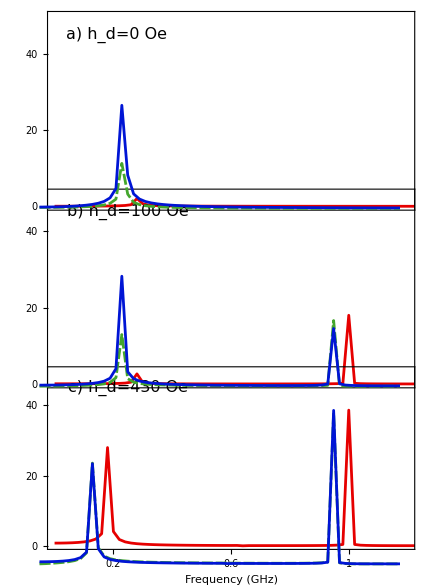

-Graphics-

No Italics, colors? dashing?

#### Time Amp Dual

```mathematica
SetDirectory["Z:\\Magnetic Research\\mathematica\\amp_files"];
```

```mathematica
AmpPlotz1=ListPlot[{Transpose[{Amptt,AmpIm[0]}],Transpose[{Amptt,AmpIm[.37]}],Transpose[{Amptt,AmpIm[.40]}],Transpose[{Amptt,AmpIm[.43]}]},
PlotRange->{{0,10000},{0,12.5}},Frame->True,
FrameStyle->Thickness[0.004],
LabelStyle->{"FontFamily"->"Arial","FontSize"->20},
FrameTicks->{
{{2500,,{0.02,0.02},{Thickness[0.004]}},{5000,,{0.02,0.02},{Thickness[0.004]}},{7500,,{0.02,0.02},{Thickness[0.004]}},{10000,,{0,0},{Thickness[0.004]}},{1250,,{0.01,0.01},{Thickness[0.004]}},{3750,,{0.01,0.01},{Thickness[0.004]}},{6250,,{0.01,0.01},{Thickness[0.004]}},{8750,,{0.01,0.01},{Thickness[0.004]}}},
{{0,0,{0.02,0},{Thickness[0.004]}},{2.5,,{0.01,0},{Thickness[0.004]}},{5,5,{0.02,0},{Thickness[0.004]}},{7.5,,{0.01,0},{Thickness[0.004]}},{10,10,{0.02,0},{Thickness[0.004]}}},None,None},
Joined->{True,True,True,True},
PlotStyle->{{Thickness[0.01],CMYKColor[.66,.38,1,0]},{Thickness[0.01],CMYKColor[0,1,0,0.4]},{Thickness[0.01],CMYKColor[0,.62,.92,0]},{Thickness[0.01],CMYKColor[1,.91,.07,.32]}},
ImagePadding->{{61,40},{60,10}},
ImageSize->500];
```

```mathematica
AmpPlotz2=ListPlot[{Transpose[{Amptt,AmpIm[0.43]}],Transpose[{Amptt,AmpIm[.46]}],Transpose[{Amptt,AmpIm[.50]}],Transpose[{Amptt,AmpIm[.70]}]},
PlotRange->{{0,10000},{0,12.5}},Frame->True,
FrameStyle->Thickness[0.004],
FrameLabel->{"Time (ns)","",None,None},
LabelStyle->{"FontFamily"->"Arial","FontSize"->20},
FrameTicks->{
{{2500,2500,{0.02,0},{Thickness[0.004]}},{5000,5000,{0.02,0},{Thickness[0.004]}},{7500,7500,{0.02,0},{Thickness[0.004]}},{10000,10000,{0,0},{Thickness[0.004]}},{1250,,{0.01,0},{Thickness[0.004]}},{3750,,{0.01,0},{Thickness[0.005]}},{6250,,{0.01,0},{Thickness[0.004]}},{8750,,{0.01,0},{Thickness[0.004]}}},
{{0,0,{0.02,0},{Thickness[0.004]}},{2.5,,{0.01,0},{Thickness[0.004]}},{5,5,{0.02,0},{Thickness[0.004]}},{7.5,,{0.01,0},{Thickness[0.004]}},{10,10,{0.02,0},{Thickness[0.004]}}},None,None},
Joined->{True,True,True,True},
PlotStyle->{{Thickness[0.01],CMYKColor[1,.91,.07,.32]},{Thickness[0.01],CMYKColor[0,0,1,0.18]},{Thickness[0.01],CMYKColor[0,1,1,0.2]},{Thickness[0.01],CMYKColor[1,.22,.11,0]}},
(*PlotStyle->{CMYKColor[1,.91,.07,.32],CMYKColor[0,0,1,0.18],CMYKColor[0,1,1,0.2],CMYKColor[1,.22,.11,0]},*)
ImagePadding->{{61,40},{60,10}},
ImageSize->500];
```

```mathematica
GraphicsColumn[{AmpPlotz1,AmpPlotz2},Spacings->-80]
```

-Graphics-

FFT Amplitude of Transient Peak (a.u), join lines

#### Theta Hx

```mathematica
SetDirectory["Z:\\Magnetic Research\\mathematica"];
```

```mathematica
thetarawdata = (Import["thetadata.dat","List"])*180/Pi;
```

```mathematica
hxAxis1 = Table[i,{i,0,.42,0.01}];
```

```mathematica
hxAxis2 = Table[i,{i,.43,1,0.01}];
```

```mathematica
thetadata1 = Transpose[{hxAxis1,Part[thetarawdata,1;;43]}];
```

```mathematica
thetadata2 = Transpose[{hxAxis2,Part[thetarawdata,44;;101]}];
```

```mathematica
thetapart1=ListPlot[thetadata1,
PlotRange->{{0,.9},{0,150}},
Frame->True,
FrameStyle->{{White,Thickness[0.004]},{White,Thickness[0.004]},{White,Thickness[0.004]},{White,Thickness[0.004]}},
FrameLabel->{"h_d (kOe)","<θ> (degrees)",None,None},
LabelStyle->{"FontFamily"->"Arial","FontSize"->20,White},
FrameTicks->{
{{.2,.2,{0,0},{Thickness[0.004]}},{.4,.4,{0,0},{Thickness[0.004]}},{.6,.6,{0,0},{Thickness[0.004]}},{.8,.8,{0,0},{Thickness[0.004]}},{1,1,{0,0},{Thickness[0.004]}},{.1,,{0,0},{Thickness[0.004]}},{.3,,{0,0},{Thickness[0.004]}},{.5,,{0,0},{Thickness[0.004]}},{.7,,{0,0},{Thickness[0.004]}},{.9,,{0,0},{Thickness[0.004]}}},
{{0,0,{0,0},{Thickness[0.004]}},{30,30,{0,0},{Thickness[0.004]}},{60,60,{0,0},{Thickness[0.004]}},{90,90,{0,0},{Thickness[0.004]}},{120,120,{0,0},{Thickness[0.004]}},{10,,{0,0},{Thickness[0.004]}},{20,,{0,0},{Thickness[0.004]}},{40,,{0,0},{Thickness[0.004]}},{50,,{0,0},{Thickness[0.004]}},{70,,{0,0},{Thickness[0.004]}},{80,,{0,0},{Thickness[0.004]}},{100,,{0,0},{Thickness[0.004]}},{110,,{0,0},{Thickness[0.004]}},{130,,{0,0},{Thickness[0.004]}},{150,150,{0,0},{Thickness[0.004]}}},None,None},
Joined->True,
(*Epilog->Inset[Show[{mtplotTheta[.42,2000,2050,0.01]},ImageSize->200],{.65,25}],*)
PlotStyle->{Thickness[0.008],CMYKColor[0,1,0,0.6]},
ImageSize->500];
```

```mathematica
thetapart2=ListPlot[thetadata2,
PlotRange->{{0,.9},{0,150}},
Frame->True,
FrameStyle->Thickness[0.004],
FrameLabel->{"h_d (kOe)","<θ> (degrees)",None,None},
LabelStyle->{"FontFamily"->"Arial","FontSize"->20},
FrameTicks->{
{{.2,.2,{0.02,0},{Thickness[0.004]}},{.4,.4,{0.02,0},{Thickness[0.004]}},{.6,.6,{0.02,0},{Thickness[0.004]}},{.8,.8,{0.02,0},{Thickness[0.004]}},{1,1,{0.02,0},{Thickness[0.004]}},{.1,,{0.01,0},{Thickness[0.004]}},{.3,,{0.01,0},{Thickness[0.004]}},{.5,,{0.01,0},{Thickness[0.004]}},{.7,,{0.01,0},{Thickness[0.004]}},{.9,,{0.01,0},{Thickness[0.004]}}},
{{0,0,{0.02,0},{Thickness[0.004]}},{30,30,{0.02,0},{Thickness[0.004]}},{60,60,{0.02,0},{Thickness[0.004]}},{90,90,{0.02,0},{Thickness[0.004]}},{120,120,{0.02,0},{Thickness[0.004]}},{10,,{0.01,0},{Thickness[0.004]}},{20,,{0.01,0},{Thickness[0.004]}},{40,,{0.01,0},{Thickness[0.004]}},{50,,{0.01,0},{Thickness[0.004]}},{70,,{0.01,0},{Thickness[0.004]}},{80,,{0.01,0},{Thickness[0.004]}},{100,,{0.01,0},{Thickness[0.004]}},{110,,{0.01,0},{Thickness[0.004]}},{130,,{0.01,0},{Thickness[0.004]}},{140,,{0.01,0},{Thickness[0.004]}},{150,150,{0.02,0},{Thickness[0.004]}}},None,None},
Joined->True,
(*Epilog->Inset[Show[{mtplotTheta[.42,2000,2050,0.01]},ImageSize->200],{.65,25}],*)
Epilog->{Thickness[0.004],Dashed,Line[{{0.425,50},{0.425,130.4}}]},
PlotStyle->{Thickness[0.008],CMYKColor[0,1,0,0.6]},
ImageSize->500];
```

```mathematica
Show[thetapart2,thetapart1]
```

Do other way with and without arrows,<>. Range from 0-1 or 0-.9?

```mathematica
mtplotTheta2[.44,2000,2051,0.01]
```

```mathematica
mtplotTheta1[.42,2000,2047,0.01]
```

```mathematica
mtplotTheta2[.44,2000,2046.02,0.01]
```

```mathematica
mtplotTheta2n[.44,2000,2046.02,0.01]
```

```mathematica
mtplotTheta1n[.42,2000,2046.02,0.01]
```

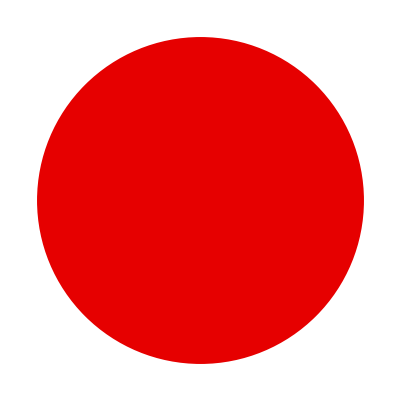

```mathematica
Graphics[{CMYKColor[0,1,1,0.1],Disk[{0,0},0.1]}]
```

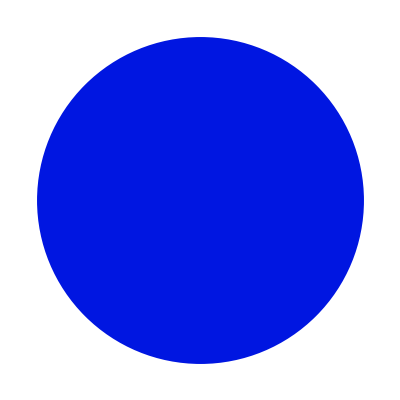

```mathematica
Graphics[{CMYKColor[1,.91,.07,.05],Disk[{0,0},0.1]}]
```

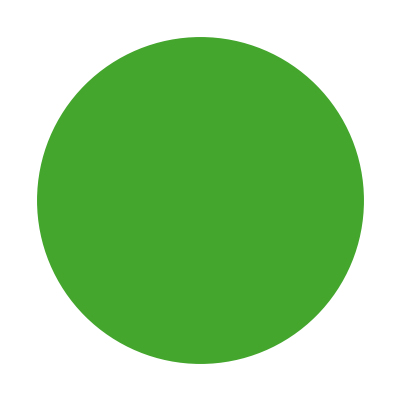

```mathematica
Graphics[{CMYKColor[.59,0,.73,0.35],Disk[{0,0},0.1]}]
```

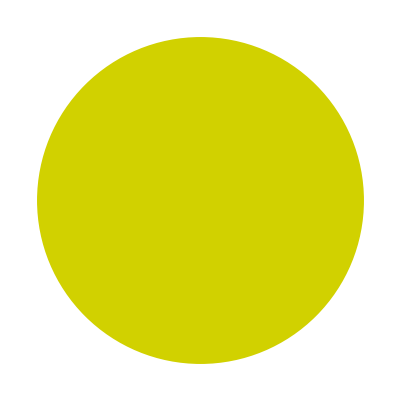

```mathematica
Graphics[{CMYKColor[0,0,1,0.18],Disk[{0,0},0.1]}]
```

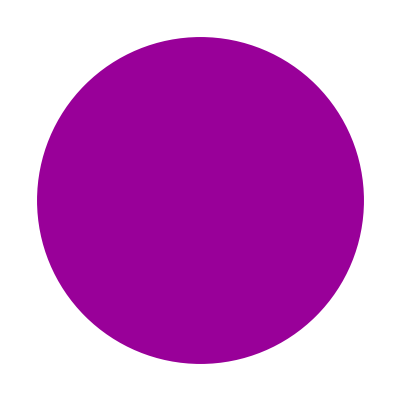

```mathematica
Graphics[{CMYKColor[0,1,0,0.4],Disk[{0,0},0.1]}]
```

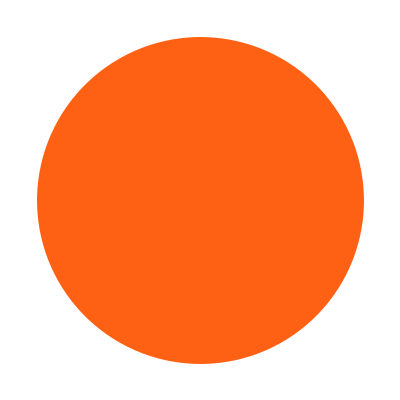

```mathematica
Graphics[{CMYKColor[0,.62,.92,0],Disk[{0,0},0.1]}]
```

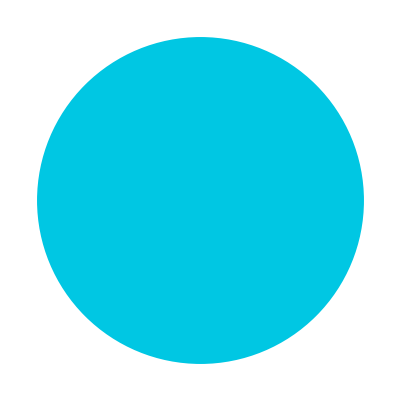

```mathematica
Graphics[{CMYKColor[1,.22,.11,0],Disk[{0,0},0.1]}]
```

```mathematica
Decay Values
```

hx = 0:
	Initial Value: 8.55570742005591
	1/e * Initial Value: 3.14747
	Decay Time: 150 ns
	Decay Time approximate: 100 ns
    
hx = 430:
	Initial Value: 8.400817078521953
	1/e * Initial Value: 3.09049
	Decay Time: 6750 ns
	Decay Time Approximate: 6750

Factor: 45

```mathematica
Parallelize[(
ytEx[0.4238,0,100000,0.1];
ytEx[0.42385,0,100000,0.1];
     ytEx[0.42389,0,100000,0.1];
ytEx[0.42392,0,100000,0.1];
)]
```

```mathematica
TimeAmpDataP[0.4238,0.1,1000]
```

```mathematica
TimeAmpDataP[0.42385,0.1,1000]
```

```mathematica
TimeAmpDataP[0.42389,0.1,1000]
```

```mathematica
TimeAmpDataP[0.42392,0.1,1000]
```

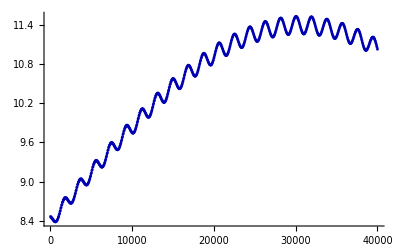

```mathematica
AmpPlotPStd[0.42395]
```

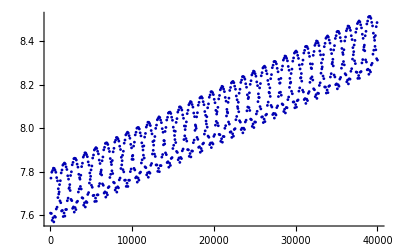

```mathematica
AmpPlotPStd[0.4238]
```

```mathematica
a :=Print["first"];
```

```mathematica
b:= Print["second"];
```

```mathematica
c :=Print["third"];
```

```mathematica
a
```

first

```mathematica
b
```

second

```mathematica
c
```

third

```mathematica
test = List[{{a},{b},{c}}]
```

first

second

third

{{{Null},{Null},{Null}}}